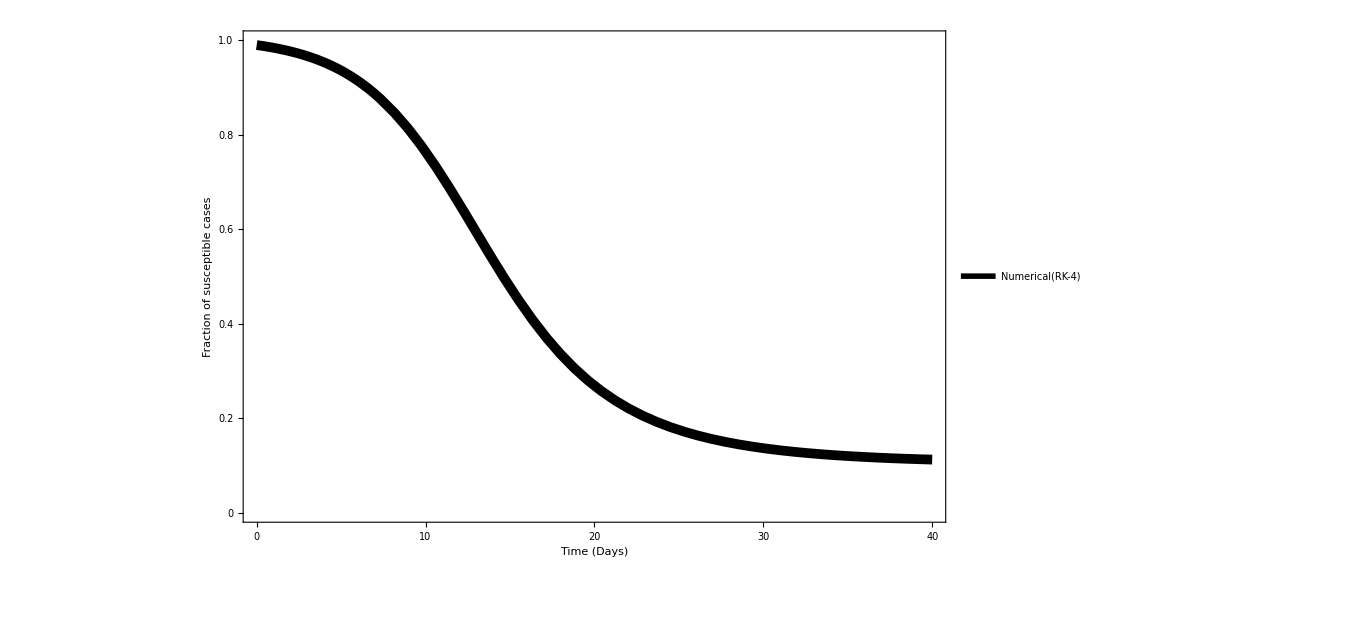

```mathematica
B=0.5; G=0.2;
Sol1=NDSolve[{S1'[t]==-B*S1[t]*I1[t],
I1'[t]== B*S1[t]*I1[t]-G*I1[t],
R1'[t]== G*I1[t],
S1[0]==0.99,I1[0]==0.01,R1[0]==0},{S1,I1,R1},{t,0,40}];
P0=Plot[{S1[t]/.Sol1},{t,0,40},PlotRange->{0,1},
PlotStyle->Directive[Black,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of susceptible cases",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[AbsoluteThickness[5]]},{Style["Numerical(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

```mathematica
S0=S1[0]/.Sol1;
I0=I1[0]/.Sol1;
R0=R1[0]/.Sol1;
```

```mathematica
C1[0]=1;
```

```mathematica
C1[k_]:=Sum[Binomial[k-1,i-1]C1[k-i]b[i],{i,k}]
```

```mathematica
b[1]=B*I0;
```

```mathematica
b[n_]:=G*b[n-1]-B*S0*Sum[Binomial[n-2,i-1]C1[n-1-i]b[i],{i,n-1}]
```

```mathematica
SolSty=Solve[1-x+(G/B)*Log[x/S0 ]==0&&x≤1,x];
Sfty=x/.SolSty
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.105894}

```mathematica
a0=Log[Sfty/S0];
Lam1=G-B*Sfty;
```

```mathematica
M10=Table[j^(i-1),{i,10},{j,10}];
b[0]=-a0;
N10=Table[b[i-1]/Lam1^(i-1),{i,10}];
Sol10=Inverse[M10].N10;
S10[x_]:=a0+Sum[Sol10[[i,1]]*Exp[-i*Lam1*x],{i,10}]
```

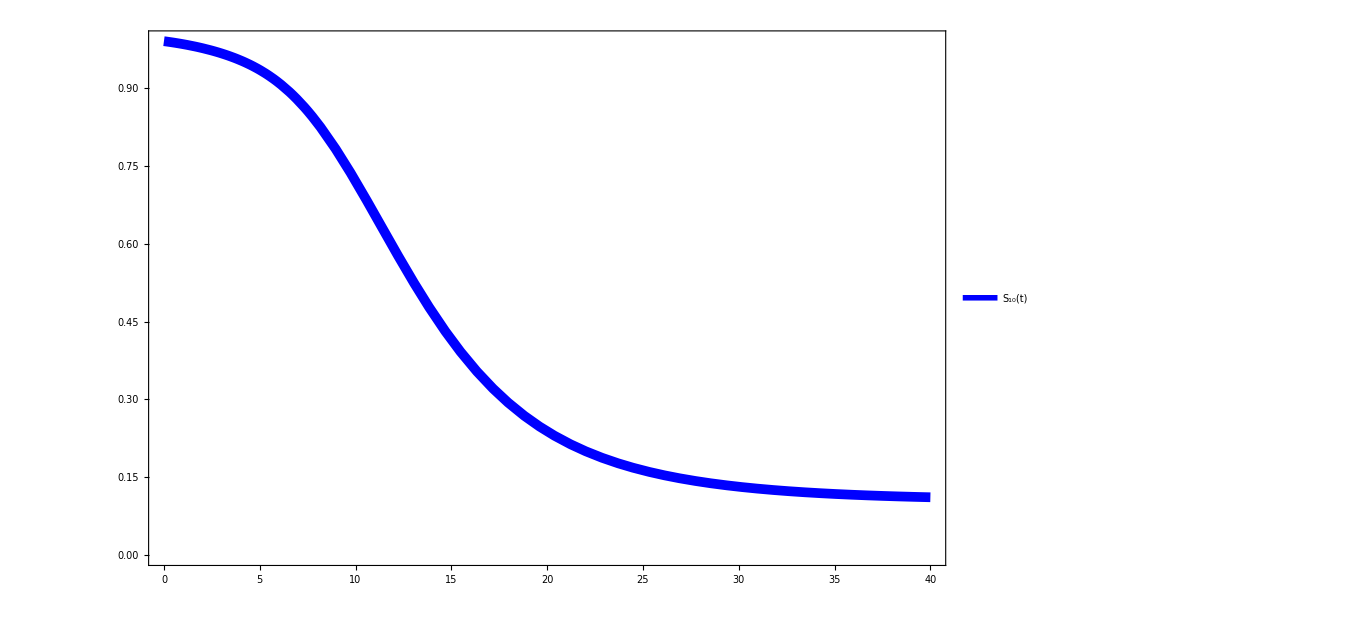

```mathematica
P10=Plot[S0*Exp[S10[x]],{x,0,40},
PlotStyle->{Blue,Thickness[0.007]},
PlotLegends-> Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]]},{Style["S_10(t)",Bold,Italic,Blue,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

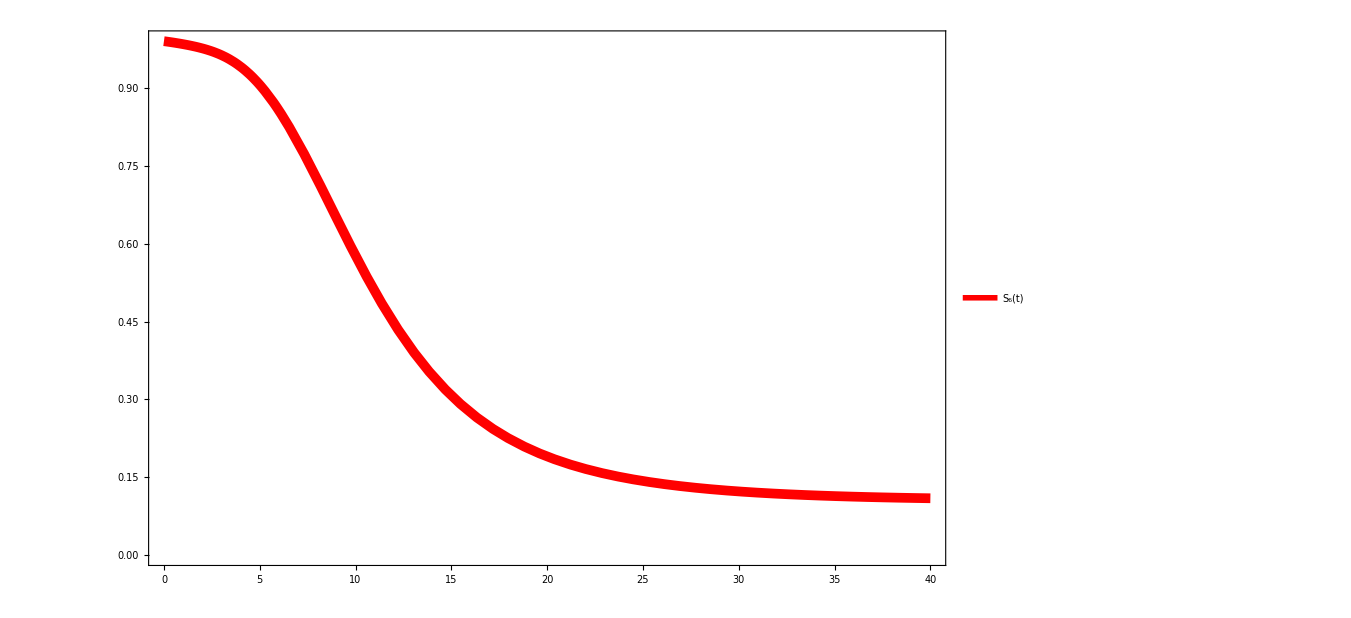

```mathematica
M6=Table[j^(i-1),{i,6},{j,6}];
b[0]=-a0;
N6=Table[b[i-1]/Lam1^(i-1),{i,6}];
Sol6=Inverse[M6].N6;
S6[x_]:=a0+Sum[Sol6[[i,1]]*Exp[-i*Lam1*x],{i,6}]
P6=Plot[S0*Exp[S6[x]],{x,0,40},
PlotStyle->{Red,Thickness[0.007]},
PlotLegends-> Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]]},{Style["S_6(t)",Bold,Italic,Red,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

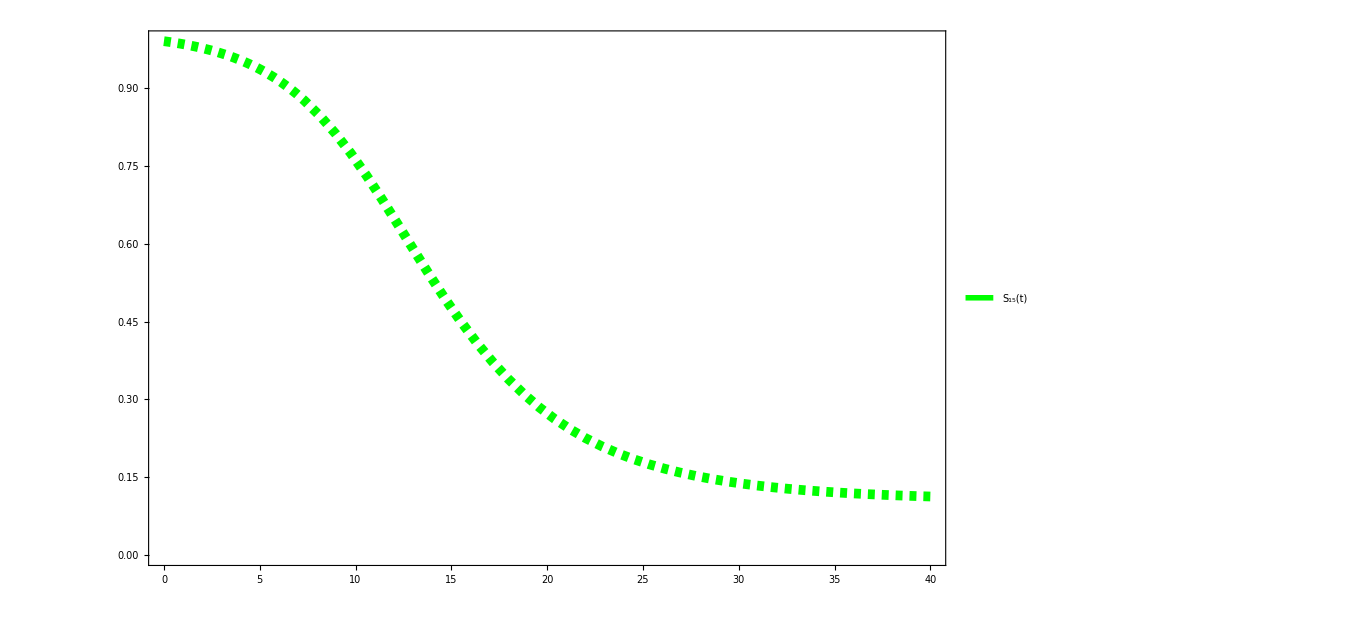

```mathematica
M15=Table[j^(i-1),{i,15},{j,15}];
N15=Table[b[i-1]/Lam1^(i-1),{i,15}];
Sol15=Inverse[M15].N15;
S15[x_]:=a0+Sum[Sol15[[i,1]]*Exp[-i*Lam1*x],{i,15}]
P15=Plot[S0*Exp[S15[x]],{x,0,40},
PlotStyle->{Green,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Green,Dashed,AbsoluteThickness[5]]},{Style["S_15(t)",Bold,Italic,Green,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

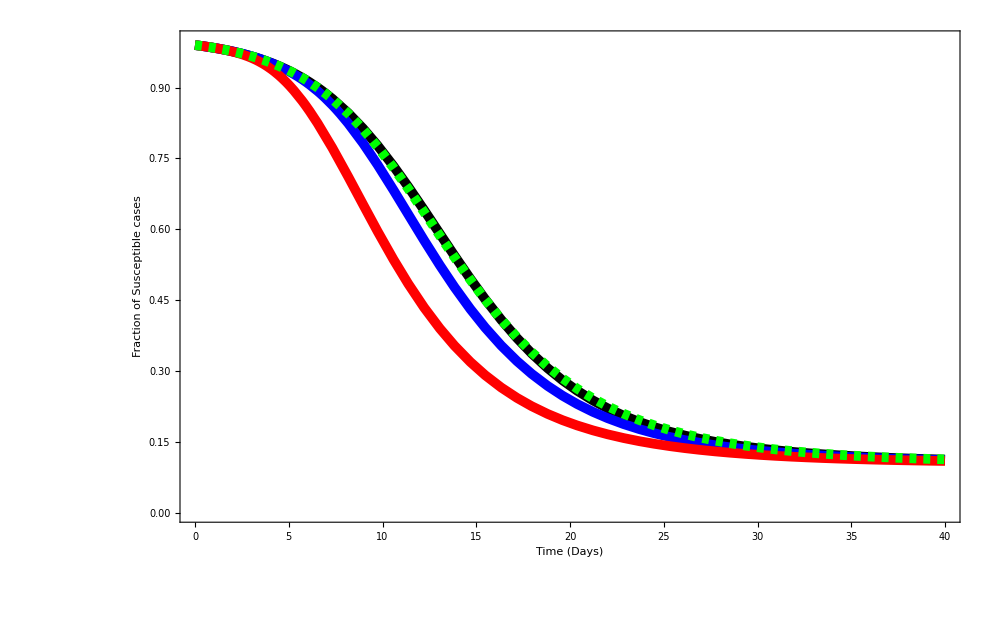

```mathematica
Show[P0,P10,P6,P15]
```

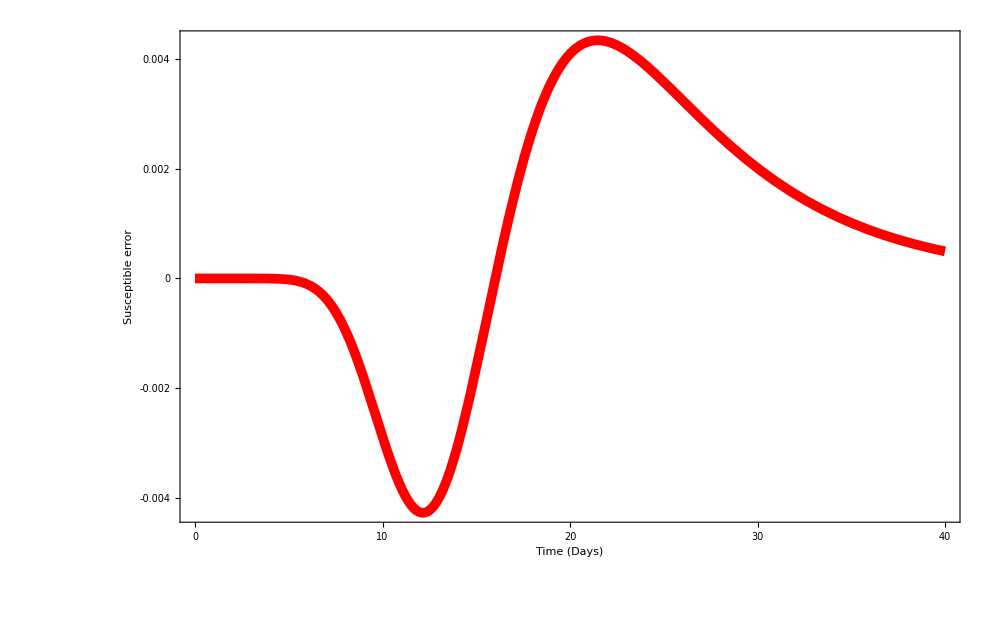

```mathematica
Plot[S0*Exp[S15[x]]-S1[x]/.Sol1,{x,0,40},
PlotStyle->Directive[Red,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->32], Style["Susceptible error",Bold,Black,FontSize->32]},
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,32],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

```mathematica
Sum[(S0*Exp[S15[x]]-S1[x]/.Sol1)^2,{x,0,40}]/41
```

{{5.88606×10^-6}}

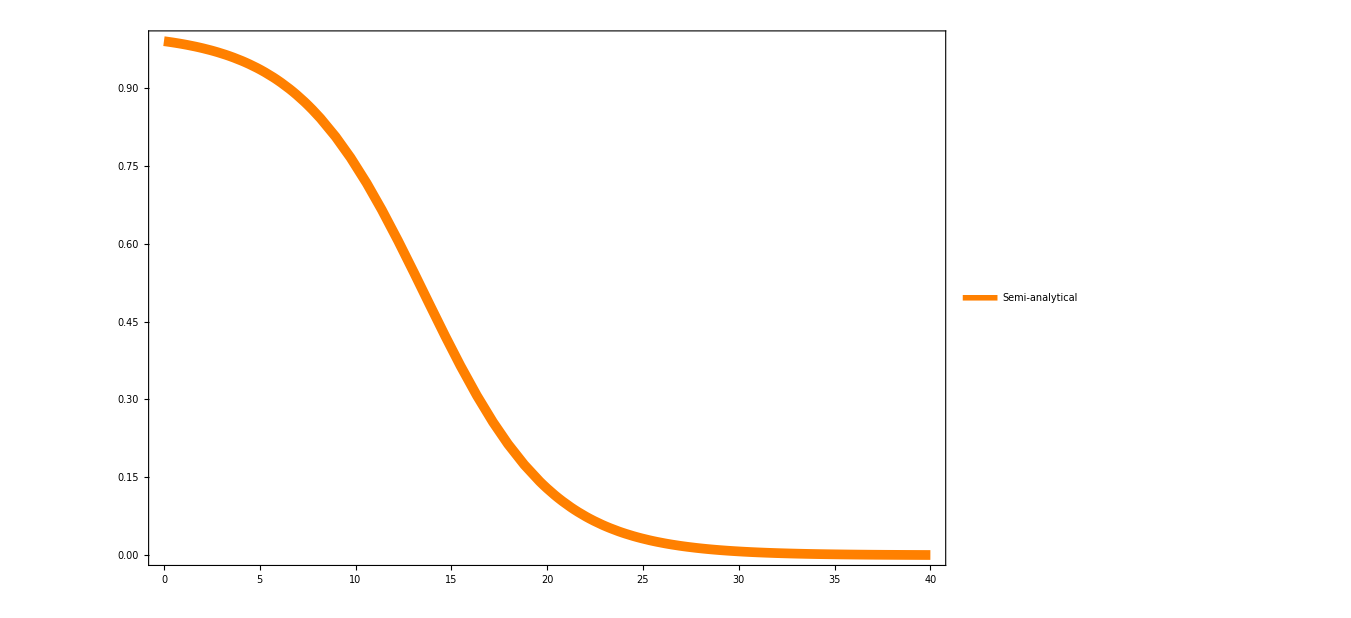

```mathematica
SS1[t_]:=(B-G)*S0/(B*(1-S0)*Exp[(B-G)*t]+B*S0-G);
SP1=Plot[SS1[t],{t,0,40},
PlotStyle->{Orange,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Orange,AbsoluteThickness[5]]},{Style["Semi-analytical",Bold,Orange,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

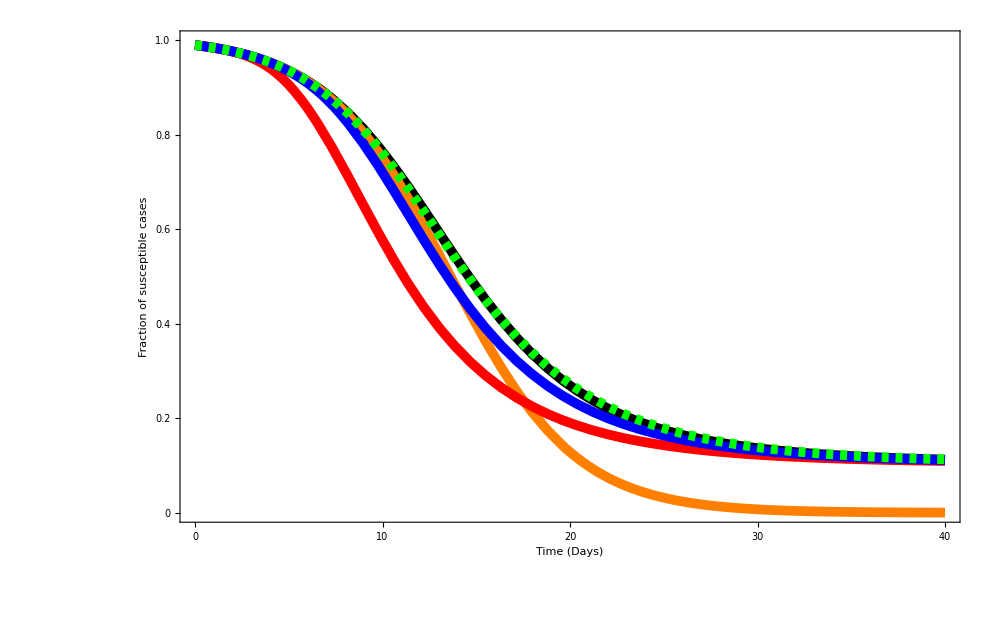

```mathematica
Show[P0,SP1,P6,P10,P15]
```

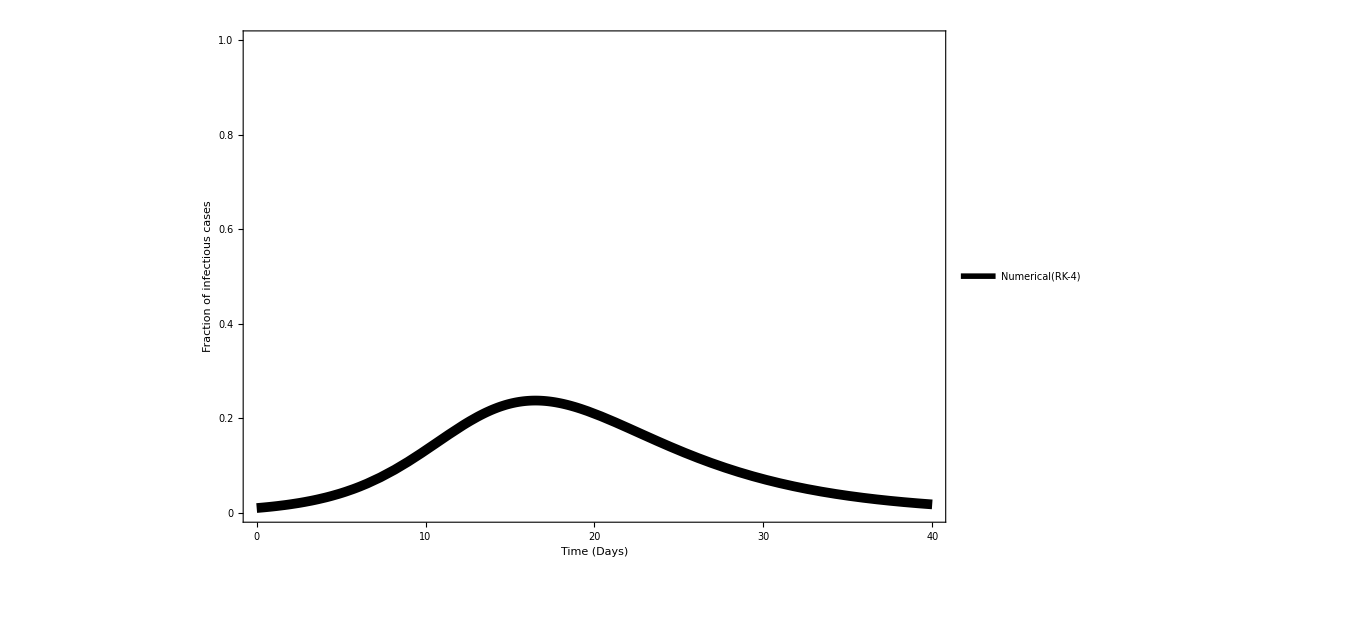

```mathematica
PI0=Plot[{I1[t]/.Sol1},{t,0,40},PlotRange->{0,1},
PlotStyle->Directive[Black,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of infectious cases",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[AbsoluteThickness[5]]},{Style["Numerical(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

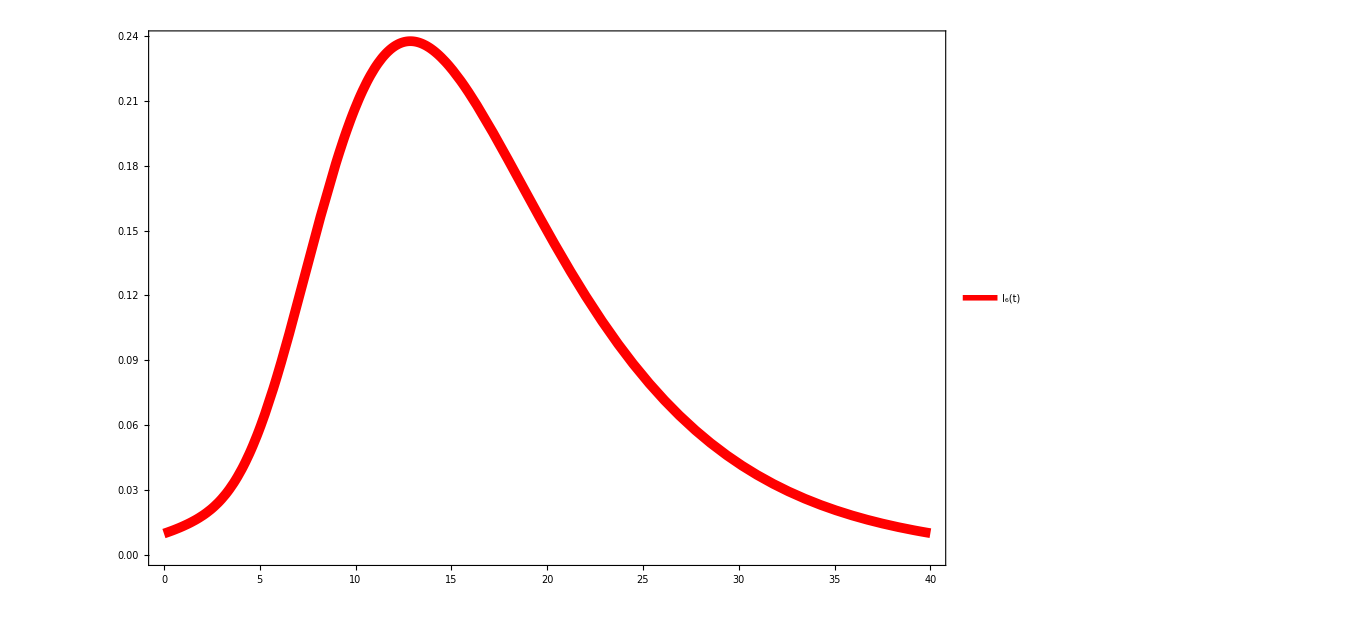

```mathematica
SS6[x_]:=S0*Exp[S6[x]]
II6[t_]:=-SS6[t]+1+(G/B)*Log[SS6[t]/S0]
PI6=Plot[II6[x],{x,0,40},
PlotStyle->{Red,Thickness[0.007]},
PlotLegends-> Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]]},{Style["I_6(t)",Bold,Italic,Red,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

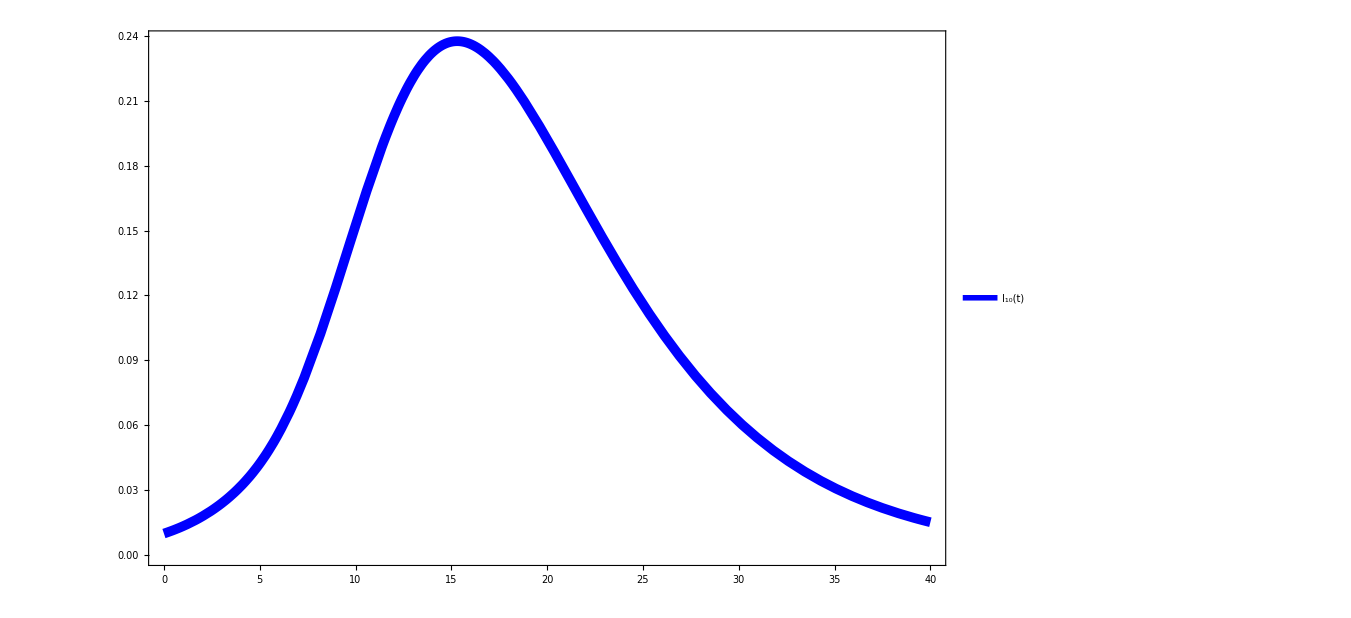

```mathematica
SS10[x_]:=S0*Exp[S10[x]]
II10[t_]:=-SS10[t]+1+(G/B)*Log[SS10[t]/S0]
PI10=Plot[II10[x],{x,0,40},
PlotStyle->{Blue,Thickness[0.007]},
PlotLegends-> Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]]},{Style["I_10(t)",Bold,Italic,Blue,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

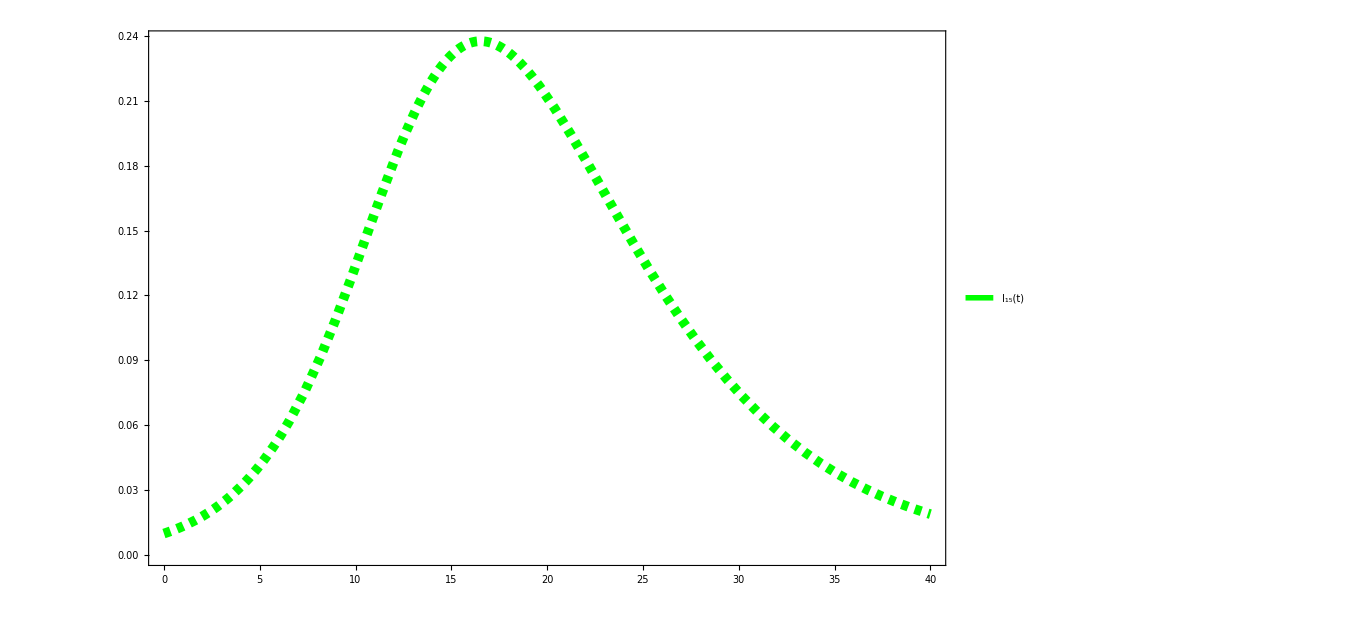

```mathematica
SS15[x_]:=S0*Exp[S15[x]]
II15[t_]:=-SS15[t]+1+(G/B)*Log[SS15[t]/S0]
PI15=Plot[II15[x],{x,0,40},
PlotStyle->{Green,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Green,Dashed,AbsoluteThickness[5]]},{Style["I_15(t)",Bold,Italic,Green,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

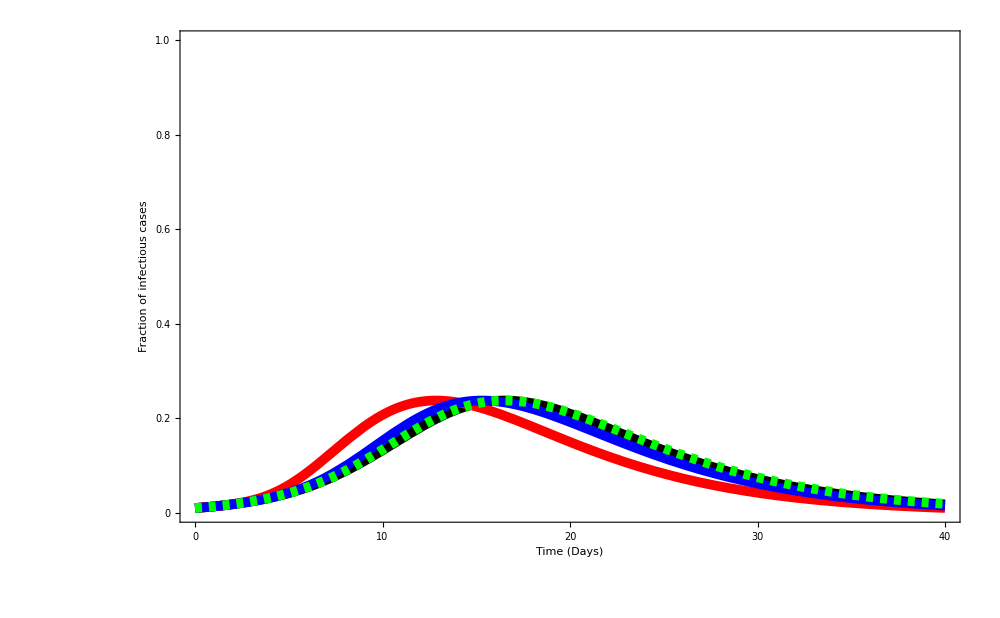

```mathematica
Show[PI0,PI6,PI10,PI15]
```

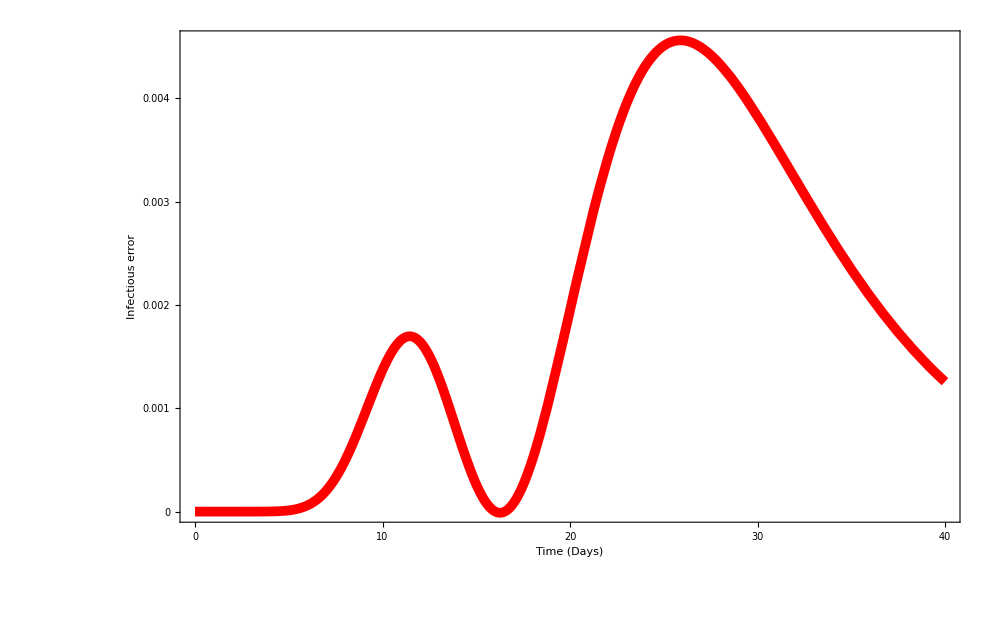

```mathematica
Plot[II15[x]-I1[x]/.Sol1,{x,0,40},
PlotStyle->Directive[Red,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->32], Style["Infectious error",Bold,Black,FontSize->32]},
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,32],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

```mathematica
Sum[(II15[x]-I1[x]/.Sol1)^2,{x,0,40}]/41
```

{{5.81967×10^-6}}

```mathematica
II0[t_]:=-SS1[t]+1+(G/B)*Log[SS1[t]/S0]
```

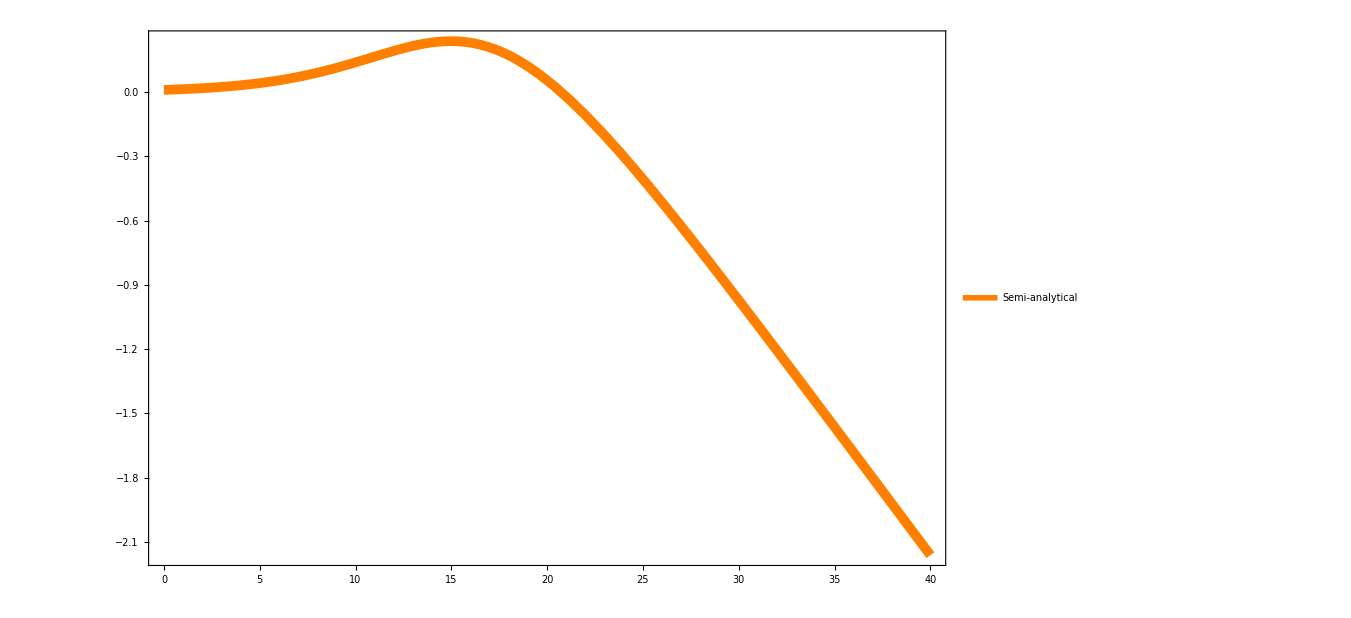

```mathematica
PIA=Plot[II0[t],{t,0,40},
PlotStyle->{Orange,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Orange,AbsoluteThickness[5]]},{Style["Semi-analytical",Bold,Orange,FontSize->36]},LegendMarkerSize->50]
,{Right,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

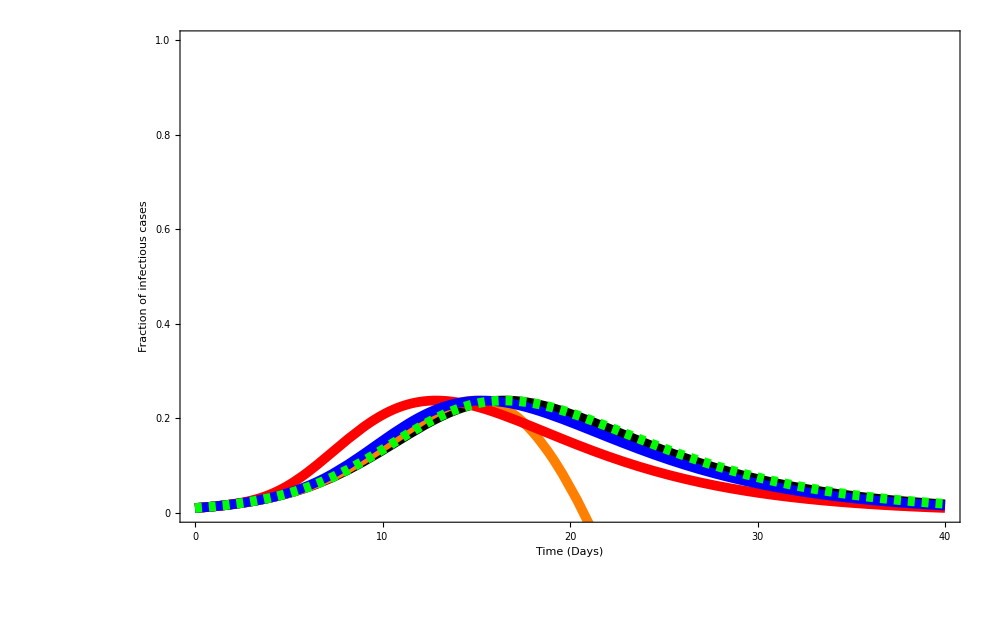

```mathematica
Show[PI0,PIA,PI6,PI10,PI15]
```

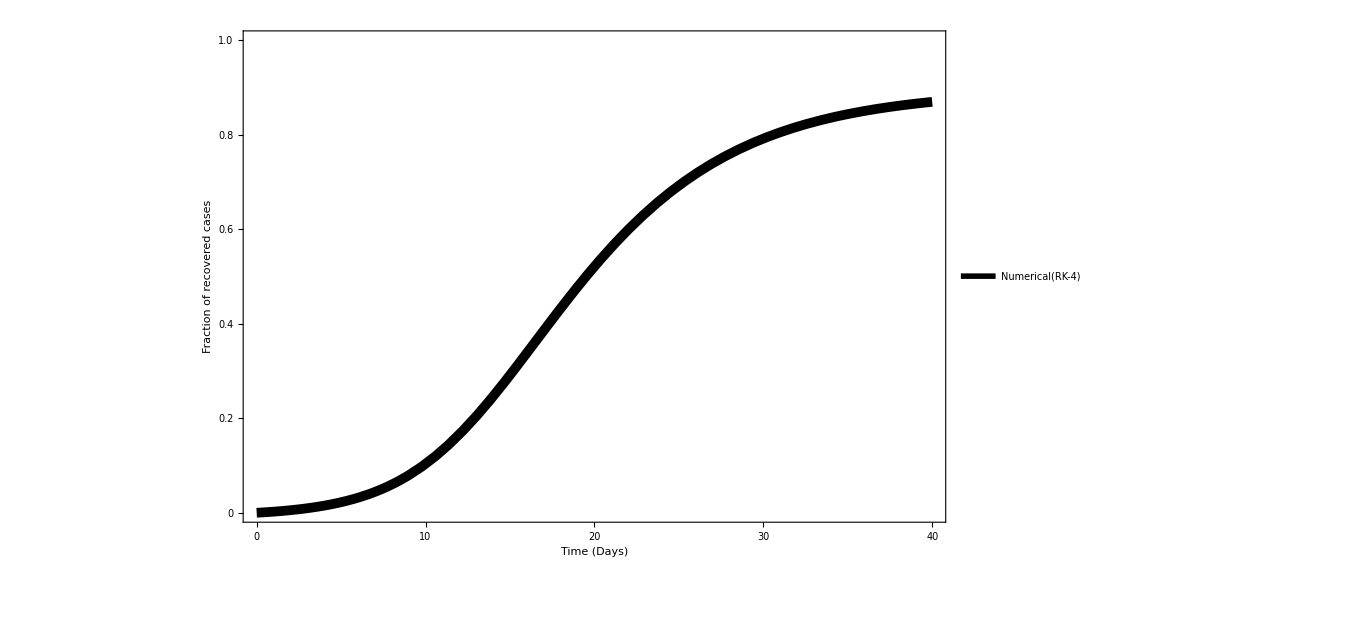

```mathematica
PR0=Plot[{R1[t]/.Sol1},{t,0,40},PlotRange->{0,1},
PlotStyle->Directive[Black,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->28], Style["Fraction of recovered cases",Bold,Black,FontSize->28]},
PlotLegends-> Placed[LineLegend[{Directive[AbsoluteThickness[5]]},{Style["Numerical(RK-4)",Bold,Black,FontSize->32]},LegendMarkerSize->50]
,{Left,Top}],
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,36],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

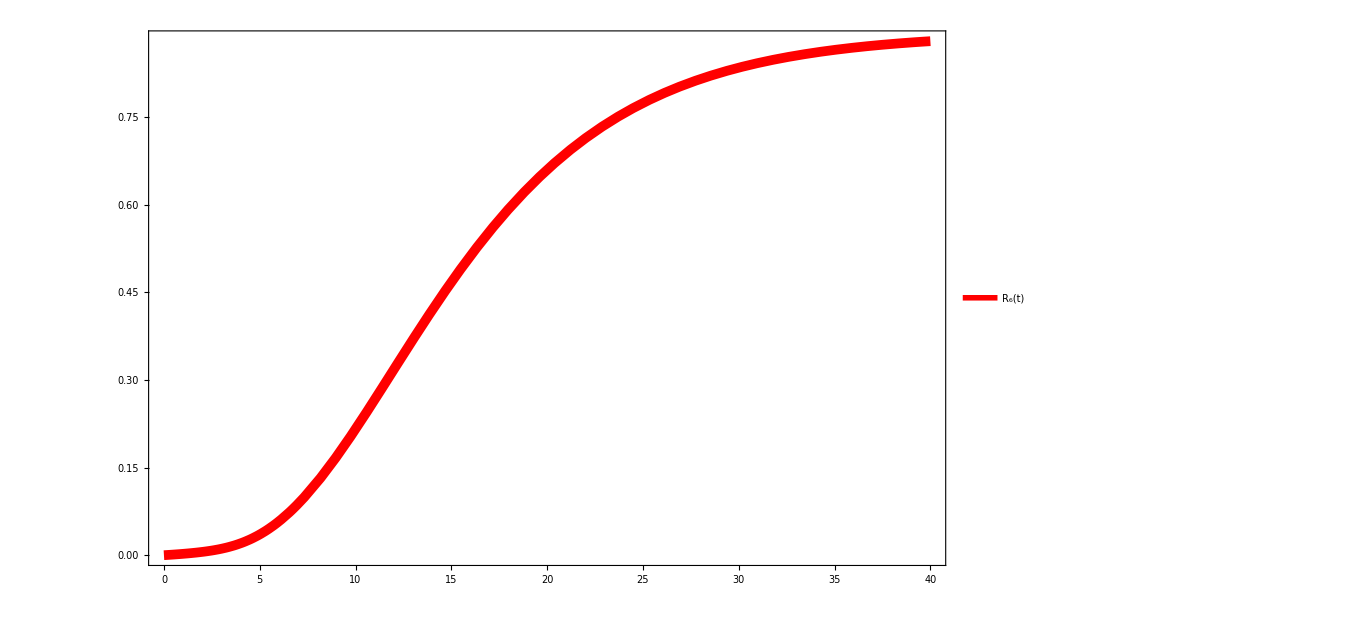

```mathematica
RR6[t_]:=(G/B)*Log[S0/SS6[t]]
PR6=Plot[RR6[x],{x,0,40},
PlotStyle->{Red,Thickness[0.007]},
PlotLegends-> Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]]},{Style["R_6(t)",Bold,Italic,Red,FontSize->36]},LegendMarkerSize->50]
,{Left,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

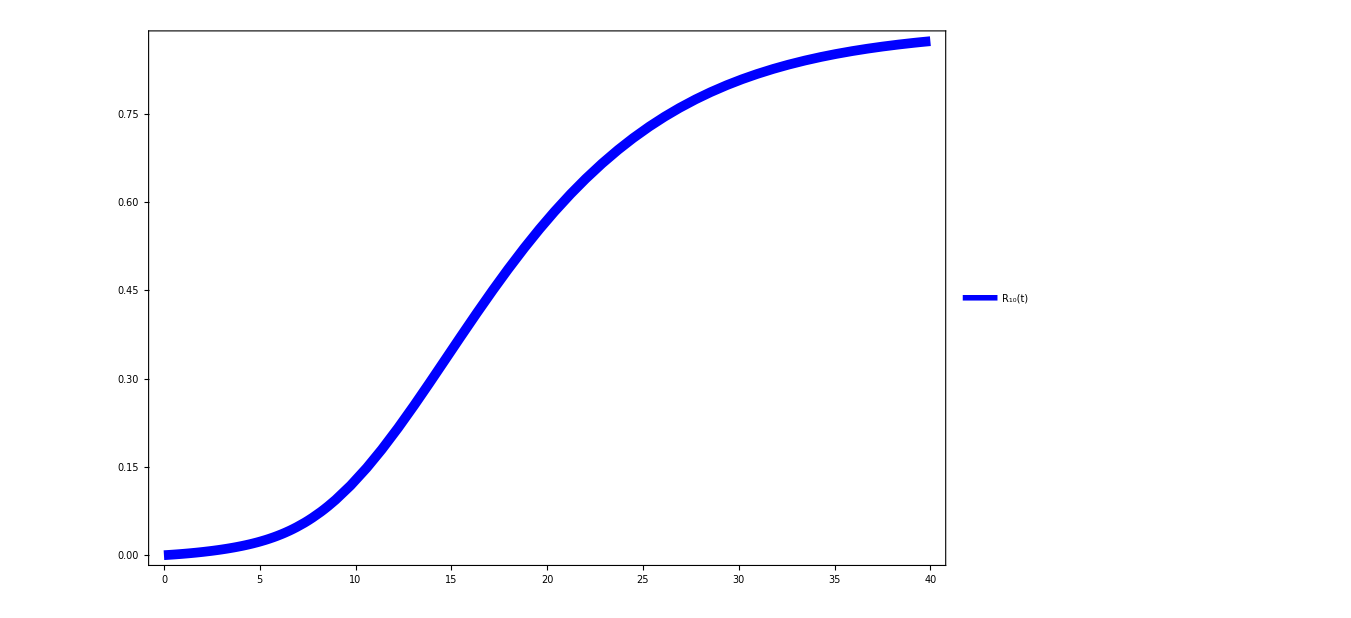

```mathematica
RR10[t_]:=(G/B)*Log[S0/SS10[t]]
PR10=Plot[RR10[x],{x,0,40},
PlotStyle->{Blue,Thickness[0.007]},
PlotLegends-> Placed[LineLegend[{Directive[Blue,AbsoluteThickness[5]]},{Style["R_10(t)",Bold,Italic,Blue,FontSize->36]},LegendMarkerSize->50]
,{Left,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

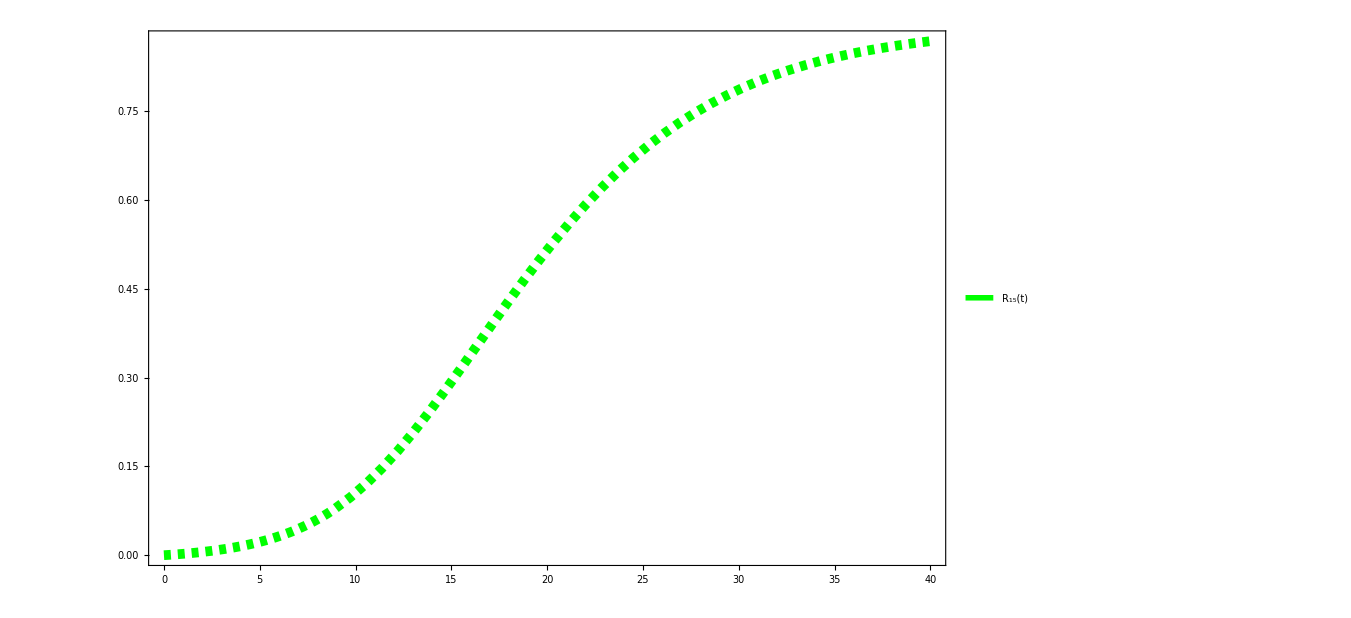

```mathematica
RR15[t_]:=(G/B)*Log[S0/SS15[t]]
PR15=Plot[RR15[x],{x,0,40},
PlotStyle->{Green,Dashed,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Green,Dashed,AbsoluteThickness[5]]},{Style["R_15(t)",Bold,Italic,Green,FontSize->36]},LegendMarkerSize->50]
,{Left,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

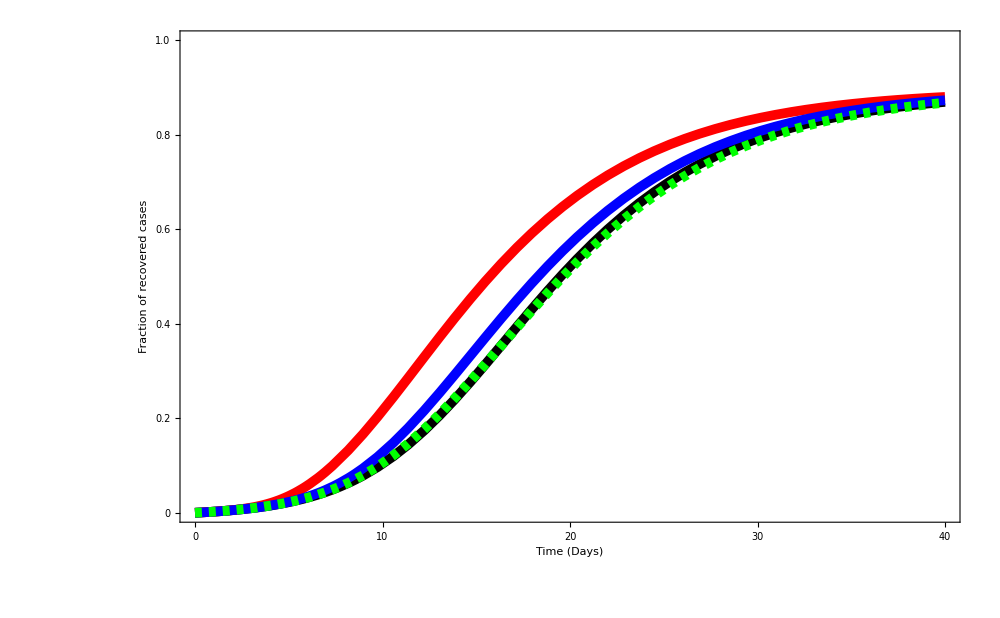

```mathematica
Show[PR0,PR6,PR10,PR15]
```

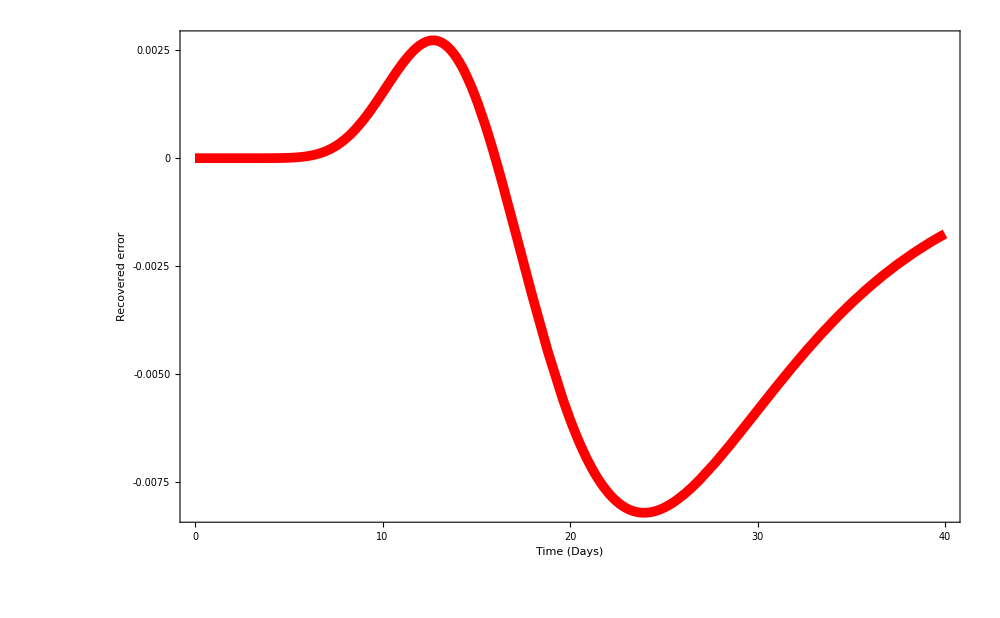

```mathematica
Plot[RR15[x]-R1[x]/.Sol1,{x,0,40},
PlotStyle->Directive[Red,Thickness[0.007]],FrameLabel->{Style["Time (Days)",Bold,Black,FontSize->32], Style["Recovered error",Bold,Black,FontSize->32]},
Frame-> True,
FrameTicksStyle->Directive[Thickness[0.004],Black,32],
FrameStyle->Directive[Thick,Black,20],
FrameTicks->{{All,Automatic},{All,Automatic}},
ImageSize->1000]
```

```mathematica
Sum[(RR15[x]-R1[x]/.Sol1)^2,{x,0,40}]/41
```

{{0.0000187405}}

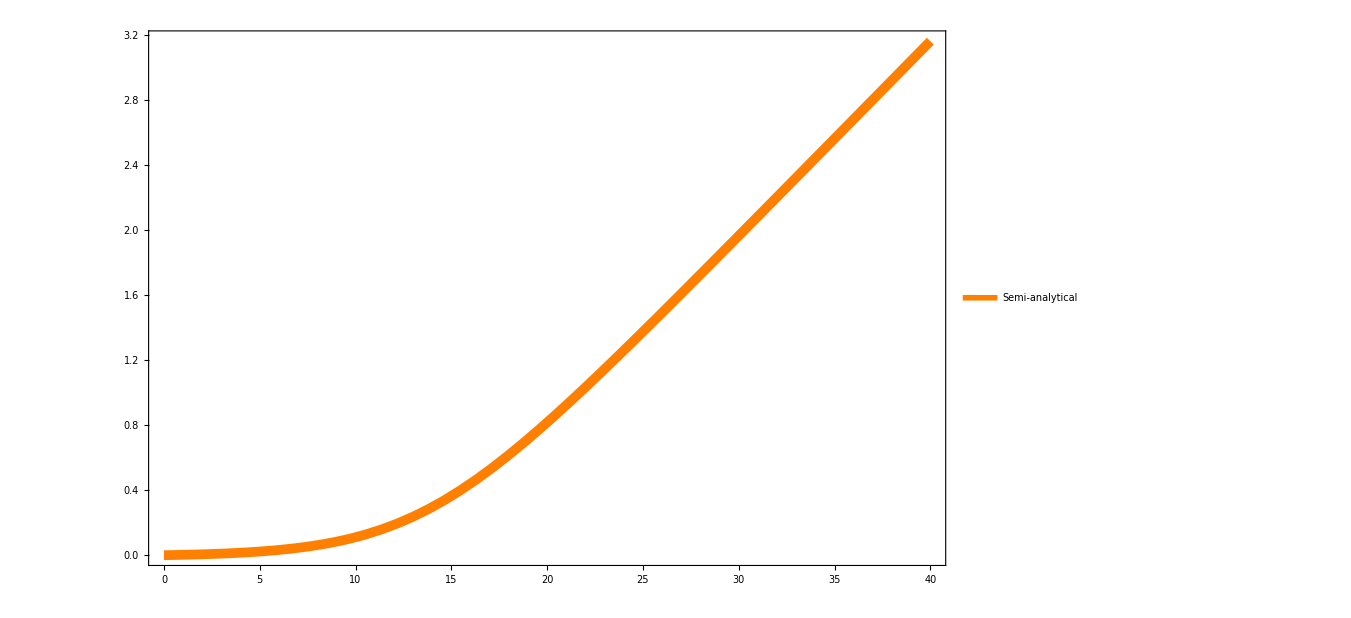

```mathematica
RR0[t_]:=(G/B)*Log[S0/SS1[t]]
PRA=Plot[RR0[t],{t,0,40},
PlotStyle->{Orange,Thickness[0.007]},PlotLegends-> Placed[LineLegend[{Directive[Orange,AbsoluteThickness[5]]},{Style["Semi-analytical",Bold,Orange,FontSize->36]},LegendMarkerSize->50]
,{Left,Top}],
Frame-> True,
FrameTicksStyle->Directive[Black,36],
FrameStyle->Directive[Thick,Black,10],
TicksStyle->Directive[100],
ImageSize->1000]
```

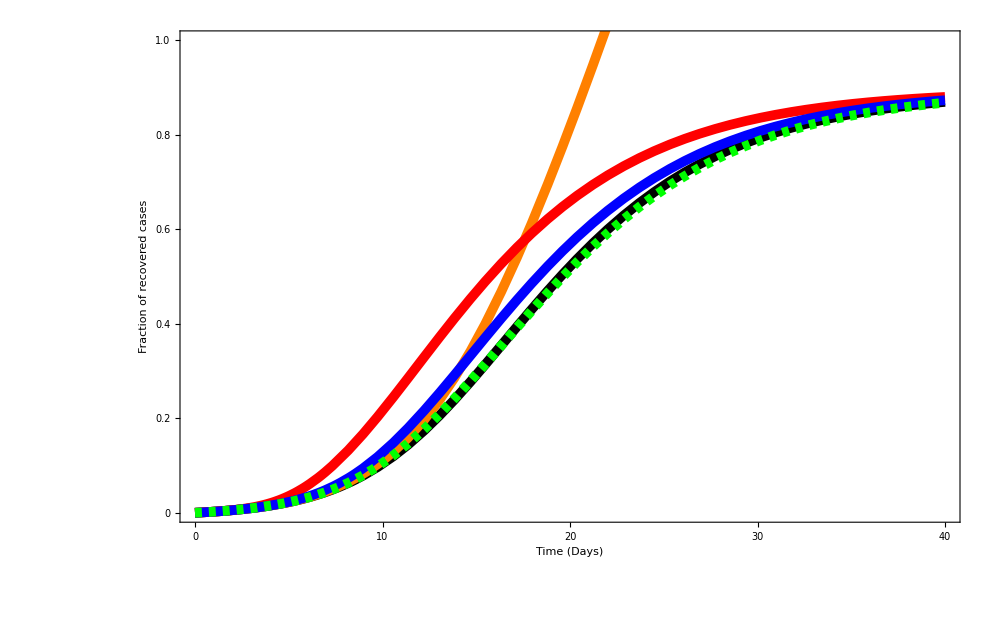

```mathematica
Show[PR0,PRA,PR6,PR10,PR15]
```